```mathematica
sandwichingSegment[num_,list_]:=Module[{ret={}},Do[If[list[[idx]]<num&&num<list[[idx+1]],ret={list[[idx]],list[[idx+1]]},],{idx,Length[list]-1}];Return[ret]]
```

```mathematica
splitIntervals[splitNumber_]:=Module[{one={0,1},two={0,1}},
Do[If[RandomInteger[{1,2}]==1,
AppendTo[one,RandomReal[]],
AppendTo[two,RandomReal[]]],{idx,1,splitNumber}];
one=Sort[one];two=Sort[two];
Return[{one,two}]]
```

```mathematica
shorterProb1[lineageNumber_,trialNumber_,separation_]:=Module[{prob={0,0}},
Do[Module[{pair=splitIntervals[lineageNumber-2],one,two,segmentIdx},
one=pair[[1]];two=pair[[2]];
segmentIdx=RandomInteger[{1,lineageNumber-2}];
If[segmentIdx>Length[one]-1-1,
If[sandwichingSegment[two[[segmentIdx-(Length[one]-1-1)+1]],one]==sandwichingSegment[two[[segmentIdx-(Length[one]-1-1)+1+separation]],one],
prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1],
If[sandwichingSegment[one[[segmentIdx+1]],two]==sandwichingSegment[one[[segmentIdx+1+separation]],two],prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1]]],
{trial,trialNumber}];prob=prob/trialNumber*1.;Return[prob]]
shorterProb2[lineageNumber_,trialNumber_,separation_]:=Module[{prob={0,0}},
Do[Module[{pair=splitIntervals[lineageNumber-2],one,two,segmentIdx},
one=pair[[1]];two=pair[[2]];
segmentIdx=RandomInteger[{1,lineageNumber-2-2separation}];
If[segmentIdx>Length[one]-1-1-separation,
If[sandwichingSegment[two[[segmentIdx-(Length[one]-1-1-separation)+1]],one]==sandwichingSegment[two[[segmentIdx-(Length[one]-1-1-separation)+1+separation]],one],
prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1],
If[sandwichingSegment[one[[segmentIdx+1]],two]==sandwichingSegment[one[[segmentIdx+1+separation]],two],prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1]]],
{trial,trialNumber}];prob=prob/trialNumber*1.;Return[prob]]
```

### Plot

```mathematica
plots=Table[Table[{recomb,shorterProb1[recomb+2,20000,separation][[1]]},{recomb,50}],{separation,6}];
```

Part::partw: Part 4 of {0,0.58805,1} does not exist.

Part::partw: Part 4 of {0,0.445313,1} does not exist.

Part::partw: Part 4 of {0,0.449093,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Print[plots]
```

{{{1,0.},{2,0.24345},{3,0.335},{4,0.371},{5,0.39855},{6,0.4183},{7,0.42425},{8,0.44305},{9,0.44305},{10,0.4462},{11,0.45785},{12,0.46065},{13,0.4645},{14,0.4666},{15,0.4684},{16,0.4753},{17,0.47135},{18,0.47445},{19,0.47835},{20,0.47305},{21,0.4738},{22,0.48485},{23,0.47185},{24,0.48385},{25,0.48255},{26,0.48235},{27,0.47875},{28,0.48075},{29,0.4861},{30,0.48145},{31,0.48095},{32,0.48355},{33,0.48555},{34,0.48405},{35,0.4869},{36,0.4889},{37,0.48945},{38,0.4885},{39,0.48875},{40,0.48865},{41,0.49175},{42,0.48855},{43,0.485},{44,0.4883},{45,0.4896},{46,0.4927},{47,0.4886},{48,0.49285},{49,0.48965},{50,0.49}},{{1,0.},{2,0.},{3,0.0851},{4,0.12435},{5,0.14795},{6,0.16275},{7,0.17695},{8,0.18645},{9,0.19485},{10,0.19805},{11,0.19915},{12,0.2077},{13,0.2119},{14,0.21185},{15,0.21985},{16,0.21815},{17,0.21945},{18,0.22615},{19,0.2273},{20,0.2225},{21,0.2278},{22,0.22605},{23,0.22755},{24,0.2269},{25,0.2334},{26,0.2283},{27,0.2303},{28,0.23645},{29,0.2295},{30,0.2365},{31,0.2314},{32,0.2355},{33,0.2365},{34,0.2371},{35,0.23835},{36,0.2374},{37,0.23875},{38,0.2356},{39,0.23565},{40,0.2355},{41,0.23475},{42,0.2393},{43,0.2417},{44,0.23975},{45,0.23975},{46,0.23405},{47,0.23975},{48,0.23875},{49,0.2434},{50,0.23895}},{{1,0.},{2,0.},{3,0.},{4,0.0309},{5,0.0505},{6,0.06075},{7,0.07305},{8,0.07915},{9,0.08385},{10,0.08975},{11,0.0915},{12,0.09355},{13,0.09135},{14,0.09435},{15,0.0979},{16,0.10115},{17,0.10695},{18,0.10465},{19,0.1061},{20,0.1057},{21,0.11},{22,0.1066},{23,0.1089},{24,0.11385},{25,0.10985},{26,0.109},{27,0.10775},{28,0.1117},{29,0.1098},{30,0.1123},{31,0.1118},{32,0.11445},{33,0.1161},{34,0.116},{35,0.11475},{36,0.10995},{37,0.11245},{38,0.11255},{39,0.11705},{40,0.1163},{41,0.1168},{42,0.11775},{43,0.11585},{44,0.11595},{45,0.11635},{46,0.1181},{47,0.114},{48,0.11455},{49,0.12135},{50,0.1145}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.013},{6,0.0217},{7,0.0265},{8,0.03065},{9,0.03345},{10,0.03815},{11,0.0379},{12,0.04115},{13,0.04235},{14,0.04815},{15,0.04395},{16,0.04645},{17,0.04925},{18,0.04745},{19,0.0501},{20,0.0495},{21,0.0506},{22,0.052},{23,0.05085},{24,0.05375},{25,0.0535},{26,0.0534},{27,0.0524},{28,0.0529},{29,0.05305},{30,0.0532},{31,0.05395},{32,0.05705},{33,0.05295},{34,0.054},{35,0.05285},{36,0.0571},{37,0.0551},{38,0.05535},{39,0.05525},{40,0.0581},{41,0.0563},{42,0.0555},{43,0.05725},{44,0.05625},{45,0.0572},{46,0.0535},{47,0.0557},{48,0.0571},{49,0.05715},{50,0.05755}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00515},{7,0.0093},{8,0.0131},{9,0.01445},{10,0.01745},{11,0.01745},{12,0.018},{13,0.0191},{14,0.02085},{15,0.021},{16,0.02165},{17,0.0205},{18,0.0214},{19,0.0225},{20,0.0227},{21,0.0221},{22,0.0235},{23,0.024},{24,0.02395},{25,0.02475},{26,0.02505},{27,0.0249},{28,0.025},{29,0.0249},{30,0.0267},{31,0.02785},{32,0.0279},{33,0.0254},{34,0.0265},{35,0.02595},{36,0.0285},{37,0.0272},{38,0.0262},{39,0.0271},{40,0.0282},{41,0.02865},{42,0.02755},{43,0.0274},{44,0.0276},{45,0.02855},{46,0.02755},{47,0.02775},{48,0.02875},{49,0.02765},{50,0.02855}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0025},{8,0.00515},{9,0.006},{10,0.00605},{11,0.00705},{12,0.00755},{13,0.00895},{14,0.009},{15,0.00935},{16,0.009},{17,0.0092},{18,0.0103},{19,0.0103},{20,0.011},{21,0.01135},{22,0.0109},{23,0.0112},{24,0.01155},{25,0.01045},{26,0.01215},{27,0.01325},{28,0.01225},{29,0.01195},{30,0.0118},{31,0.01125},{32,0.0118},{33,0.0127},{34,0.01235},{35,0.013},{36,0.01275},{37,0.01455},{38,0.01355},{39,0.01265},{40,0.01395},{41,0.0124},{42,0.01315},{43,0.01465},{44,0.0141},{45,0.0132},{46,0.0143},{47,0.0139},{48,0.0142},{49,0.01385},{50,0.0128}}}

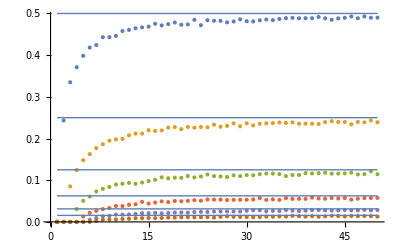

```mathematica
Show[ListPlot[plots],Plot[Table[1/2^separation,{separation,6}],{recomb,1,50},PlotStyle->Thin]]
```

### Old versions

```mathematica
shorterProb[lineageNumber_,trialNumber_,separation_]:=Module[{prob={0,0}},
Do[Module[{pair=splitIntervals[lineageNumber-2],one,two,segmentNumbers={0,0},segment},
one=pair[[1]];two=pair[[2]];
segmentNumbers[[1]]=Max[{0,Length[one]-1-1-separation}];
segmentNumbers[[2]]=Max[{0,Length[two]-1-1-separation}];
If[Total[segmentNumbers]>0,
segment=RandomInteger[{1,Total[segmentNumbers]}];
If[segment>segmentNumbers[[1]],
If[sandwichingSegment[two[[segment-segmentNumbers[[1]]+1]],one]==sandwichingSegment[two[[segment-segmentNumbers[[1]]+1+separation]],one],
prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1],
If[sandwichingSegment[one[[segment+1]],two]==sandwichingSegment[one[[segment+1+separation]],two],prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1]],Print["Not enough segments."]
]],
{trial,trialNumber}];prob=prob/trialNumber*1.;Return[prob]]
```